```mathematica
(*This script performs calculations relating to the BTSP model with correlated activity and uncorrelated plateaus, including the stochastic matrix describing the state transitions, its eigenvectors and eigenvalues, the resulting signal to noise ratio for pattern retrieval, and confusion between patterns.*)

M=Transpose[{{(1-fu)(1-fp^2),fu(1-fp),0,0,0,0,fp^2(1-fu),0,fu*fp(1-fp),fp^2*fu},{fd(1-fp^2),(1-fd)(1-fp),0,0,0,0,fp^2fd,0,fp(1-fp)(1-fd),fp^2(1-fd)},{0,0,(1-fp)^2(1-fu),fp(1-fp)(1-fu), fp(1-fp)(1-fu),(1-fp)^2fu,fp^2(1-fu), fp(1-fp)fu, fp(1-fp)fu, fu*fp^2},{fp(1-fu),fp*fu,(1-fp)^2(1-fu),fp(1-fp)(1-fu),0,fu(1-fp)^2,0,fp(1-fp)fu,0,0},{fp(1-fu),fu,(1-fp)^2(1-fu),0,fp(1-fp)(1-fu),0,0,0,0,0},{fp*fd,fp(1-fd),(1-fp)^2fd, fp(1-fp)fd,0,(1-fp)^2(1-fd),0,fp(1-fp)(1-fd),0,0},{(2fp-fp^2)(1-fu),fu,(1-fp)^2(1-fu),0,0,0,0,0,0,0},{fp*fd,fp(1-fd),(1-fp)^2fd,fp(1-fp)fd,0,(1-fp)^2(1-fd),0,fp(1-fp)(1-fd),0,0}, {(2fp-fp^2)fd,1-fd,(1-fp)^2fd,0,0,0,0,0,0,0},{(2fp-fp^2)fd,1-fd,(1-fp)^2fd,0,0,0,0,0,0,0}}];
```

```mathematica
(*fu is probability of going from the down-state to the up-state, fd probability of going from up-state to down-state, fp is the probability of a plateau*)
```

```mathematica
MatrixForm[M]
```

((1-fp^2) (1-fu) | fd (1-fp^2) | 0 | fp (1-fu) | fp (1-fu) | fd fp | (2 fp-fp^2) (1-fu) | fd fp | fd (2 fp-fp^2) | fd (2 fp-fp^2)
(1-fp) fu | (1-fd) (1-fp) | 0 | fp fu | fu | (1-fd) fp | fu | (1-fd) fp | 1-fd | 1-fd
0 | 0 | (1-fp)^2 (1-fu) | (1-fp)^2 (1-fu) | (1-fp)^2 (1-fu) | fd (1-fp)^2 | (1-fp)^2 (1-fu) | fd (1-fp)^2 | fd (1-fp)^2 | fd (1-fp)^2
0 | 0 | (1-fp) fp (1-fu) | (1-fp) fp (1-fu) | 0 | fd (1-fp) fp | 0 | fd (1-fp) fp | 0 | 0
0 | 0 | (1-fp) fp (1-fu) | 0 | (1-fp) fp (1-fu) | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-fp)^2 fu | (1-fp)^2 fu | 0 | (1-fd) (1-fp)^2 | 0 | (1-fd) (1-fp)^2 | 0 | 0
fp^2 (1-fu) | fd fp^2 | fp^2 (1-fu) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-fp) fp fu | (1-fp) fp fu | 0 | (1-fd) (1-fp) fp | 0 | (1-fd) (1-fp) fp | 0 | 0
(1-fp) fp fu | (1-fd) (1-fp) fp | (1-fp) fp fu | 0 | 0 | 0 | 0 | 0 | 0 | 0
fp^2 fu | (1-fd) fp^2 | fp^2 fu | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Total[M] //Simplify (*Check normalization of stochastic matrix*)
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
MatrixForm[M /. {fu->f, fd->1-f,fp->f}]
```

((1-f) (1-f^2) | (1-f) (1-f^2) | 0 | (1-f) f | (1-f) f | (1-f) f | (1-f) (2 f-f^2) | (1-f) f | (1-f) (2 f-f^2) | (1-f) (2 f-f^2)
(1-f) f | (1-f) f | 0 | f^2 | f | f^2 | f | f^2 | f | f
0 | 0 | (1-f)^3 | (1-f)^3 | (1-f)^3 | (1-f)^3 | (1-f)^3 | (1-f)^3 | (1-f)^3 | (1-f)^3
0 | 0 | (1-f)^2 f | (1-f)^2 f | 0 | (1-f)^2 f | 0 | (1-f)^2 f | 0 | 0
0 | 0 | (1-f)^2 f | 0 | (1-f)^2 f | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-f)^2 f | (1-f)^2 f | 0 | (1-f)^2 f | 0 | (1-f)^2 f | 0 | 0
(1-f) f^2 | (1-f) f^2 | (1-f) f^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-f) f^2 | (1-f) f^2 | 0 | (1-f) f^2 | 0 | (1-f) f^2 | 0 | 0
(1-f) f^2 | (1-f) f^2 | (1-f) f^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
f^3 | f^3 | f^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
evals=Eigenvalues[M];
evalsreduce=evals/. fu->fa/(1-fa)*fd /. fd->1-(1+0)fa /. fa->fp;
evalsreduce2=evals/. fu->fa/(1-fa)*fd /. fd->(1-c)(1-fa) /.fa->fp;
```

```mathematica
evalsreduce /. fp->0.01  (*check which eigenvalue is the second largest*)
```

{1,0,0,0,-0.0139012,0.,0.,0.000193128,0.0138955,0.999415}

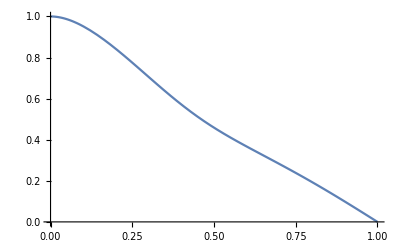

```mathematica
Plot[evalsreduce[[10]],{fp,0,1}]
```

```mathematica
evalsreduce2 /. fp->.01  /. c->0
(*ContourPlot[evalsreduce2[[10]],{fp,0,1},{c,-1,1},Axes->True,AxesLabel->{fp,c},PlotLegends->Automatic]*)
```

{1,0,0,0.,-0.0139012,0.,0.,0.000193128,0.0138955,0.999415}

```mathematica
Series[evalsreduce[[10]],{fp,0,3}] (*Check the sparse limit approximation of the second eigenvalue when c goes to zero*)
```

1-6 fp^2+15 fp^3+O[fp]^4

```mathematica
Series[evalsreduce2[[10]]//ToRadicals,{fp,0,3}] (*Attempt to check sparse limit with non-zero c, gives wrong branch cut*)
```

Root::sbr: Because of branch cuts, the series may represent a different root of c^2 fp^5-7 c^2 fp^6+2 c^3 fp^6+21 c^2 fp^7-12 c^3 fp^7+«26»+(c^2 fp+2 fp^2-3 c^2 fp^2+c^3 fp^2-7 fp^3+5 c fp^3+3 c^2 fp^3-3 c^3 fp^3+9 fp^4-16 c fp^4+4 c^3 fp^4-5 fp^5+16 c fp^5-4 c^2 fp^5-3 c^3 fp^5+fp^6-5 c fp^6+3 c^2 fp^6+c^3 fp^6) #1^3+(c-2 c fp-c^2 fp-4 c fp^2+3 c^2 fp^2-6 fp^3+14 c fp^3-6 c^2 fp^3+13 fp^4-18 c fp^4+7 c^2 fp^4-9 fp^5+14 c fp^5-5 c^2 fp^5+2 fp^6-4 c fp^6+2 c^2 fp^6) #1^4+(-1-c+2 c fp+4 fp^2-2 c fp^2-2 fp^3+2 c fp^3) #1^5+#1^6& for some values of {c,fp}.

c-c fp+((1+c-c^2) fp^2)/c+((5-8 c^2+4 c^3) fp^3)/((-1+c) c)+O[fp]^4

```mathematica
evalsreduce2 /. fp->.01 /.c->.5(* check that λ2 is still the last entry when c isn't zero *)
```

{1,0,0,0.5,-0.010019,-0.00492991,0.0000979822,0.00982568,0.495237,0.99949}

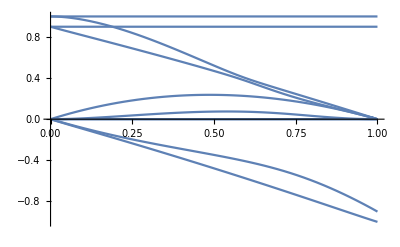

```mathematica
Plot[evalsreduce2 /. c->.9,{fp,0,1}] (*for any fixed value of c, in the sparse limit, λ2 is the second eigenvalue*)
```

```mathematica
evalsreduce2 /. c->.9 /. fp->.01
```

{1,0,0,0.9,-0.00992363,-0.00897986,0.0000979319,0.00988955,0.891107,0.999589}

```mathematica
m=M/. fu->(1-c)fa /. fd->(1-c)(1-fa) ;
```

```mathematica
MatrixForm[m]
evals=Eigenvalues[m];
```

((1-(1-c) fa) (1-fp^2) | (1-c) (1-fa) (1-fp^2) | 0 | (1-(1-c) fa) fp | (1-(1-c) fa) fp | (1-c) (1-fa) fp | (1-(1-c) fa) (2 fp-fp^2) | (1-c) (1-fa) fp | (1-c) (1-fa) (2 fp-fp^2) | (1-c) (1-fa) (2 fp-fp^2)
(1-c) fa (1-fp) | (1-(1-c) (1-fa)) (1-fp) | 0 | (1-c) fa fp | (1-c) fa | (1-(1-c) (1-fa)) fp | (1-c) fa | (1-(1-c) (1-fa)) fp | 1-(1-c) (1-fa) | 1-(1-c) (1-fa)
0 | 0 | (1-(1-c) fa) (1-fp)^2 | (1-(1-c) fa) (1-fp)^2 | (1-(1-c) fa) (1-fp)^2 | (1-c) (1-fa) (1-fp)^2 | (1-(1-c) fa) (1-fp)^2 | (1-c) (1-fa) (1-fp)^2 | (1-c) (1-fa) (1-fp)^2 | (1-c) (1-fa) (1-fp)^2
0 | 0 | (1-(1-c) fa) (1-fp) fp | (1-(1-c) fa) (1-fp) fp | 0 | (1-c) (1-fa) (1-fp) fp | 0 | (1-c) (1-fa) (1-fp) fp | 0 | 0
0 | 0 | (1-(1-c) fa) (1-fp) fp | 0 | (1-(1-c) fa) (1-fp) fp | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-c) fa (1-fp)^2 | (1-c) fa (1-fp)^2 | 0 | (1-(1-c) (1-fa)) (1-fp)^2 | 0 | (1-(1-c) (1-fa)) (1-fp)^2 | 0 | 0
(1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-c) fa (1-fp) fp | (1-c) fa (1-fp) fp | 0 | (1-(1-c) (1-fa)) (1-fp) fp | 0 | (1-(1-c) (1-fa)) (1-fp) fp | 0 | 0
(1-c) fa (1-fp) fp | (1-(1-c) (1-fa)) (1-fp) fp | (1-c) fa (1-fp) fp | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-c) fa fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

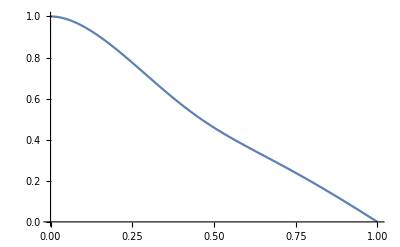

```mathematica
Plot[evals[[10]] /.c->0 /. fa->fp,{fp,0,1}]
```

```mathematica
λ2=evals[[10]];
```

```mathematica
Series[λ2,{fp,0.01,3}]
```

General::munfl: -1.51322644965817×10^-439 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.53486155710503×10^-451 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.11894044198319×10^-474 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Root::sbr: Because of branch cuts, the series may represent a different root of c^2 fp^5-2 c^2 fa fp^5+2 c^3 fa fp^5+«53»+(c-2 c fp-c^2 fp-2 c fa fp+2 c^2 fa fp-fa^2 fp+2 c fa^2 fp-c^2 fa^2 fp-2 c fp^2+c^2 fp^2-3 fa fp^2+8 c fa fp^2-5 c^2 fa fp^2+4 fa^2 fp^2-8 c fa^2 fp^2+4 c^2 fa^2 fp^2-2 fp^3+4 c fp^3+7 fa fp^3-10 c fa fp^3+3 c^2 fa fp^3-5 fa^2 fp^3+10 c fa^2 fp^3-5 c^2 fa^2 fp^3+2 fp^4-4 fa fp^4+4 c fa fp^4+2 fa^2 fp^4-4 c fa^2 fp^4+2 c^2 fa^2 fp^4) #1^4+(-1-c+2 c fp+2 fa fp-2 c fa fp+2 fp^2-2 fa fp^2+2 c fa fp^2) #1^5+#1^6& for some values of {c,fa,fp}.

Root[9.5099×10^-11 c^2-1.90198×10^-10 c^2 fa+1.90198×10^-10 c^3 fa+7+(-1.98×10^-6+0.979804 c-0.0099 c^2-0.00029304 fa-0.01921 c fa+0.019503 c^2 fa-0.00960498 fa^2+0.01921 c fa^2-0.00960498 c^2 fa^2) #1^4+(-0.9998-0.98 c+0.0198 fa-0.0198 c fa) #1^5+#1^6&,6]+(6.64953×10^-24 (1) (fp-0.01))/(-4.63101×10^102 c+87)+(60 (1) 1^3)/(-67 c^2+9474+1)+O[fp-0.01]^4
 |  |  |  |

```mathematica
evl=Eigenvectors[Transpose[m]];
```

```mathematica
evr=Eigenvectors[m];
```

```mathematica
evl1=evl[[1]];
evl2=evl[[10]];
```

```mathematica
evr2=evr[[10]];
evr1=evr[[1]];
evr1=evr1/Total[evr1*evl1];
evr2=evr2/Total[evr2*evl2];
```

```mathematica
(*ContourPlot[1-evr1[[1]]-evr1[[2]],{fp,0,1},{c,-1,1},Axes->True,AxesLabel->{"fp","c"},PlotLegends->Automatic,Background->White]*)
```

```mathematica
w=1-evr1[[1]]-evr1[[2]]; (*this is the average value of the weights in steady state as a function of the variables fp, fa, c *)
```

```mathematica
w //Simplify
```

((-1+c)^2 fa^3 (-1+fp)^4 fp (1+c^2 (-1+fp) fp^2)-fp (1-fp+fp^2)^2 (1+c^2 (-1+fp) fp+c (-1+2 fp))+fa (-1+2 fp-2 fp^2+fp^3) (1-2 fp+3 fp^2+c (-2+4 fp-6 fp^2+4 fp^3)+c^3 fp^2 (1-2 fp+3 fp^2-3 fp^3+fp^4)+c^2 (1-2 fp+fp^2-2 fp^4+fp^5))+fa^2 (-1+fp)^2 (1-3 fp+4 fp^2-c^3 (-1+fp)^5 fp^2-3 fp^3+c^4 (-1+fp)^2 fp^3 (1-fp+fp^2)+c (-2+6 fp-8 fp^2+7 fp^3-2 fp^4)+c^2 (1-3 fp+3 fp^2-5 fp^4+6 fp^5-2 fp^6)))/((-1+c)^4 fa^4 (-1+fp)^6 fp+fp (-3+4 fp-2 fp^2-4 fp^3+6 fp^4-4 fp^5+fp^6) (1+c^2 (-1+fp) fp+c (-1+2 fp))+(-1+c)^3 fa^3 (-1+fp)^5 fp (-2+4 fp+c (2-fp+2 fp^2))+(-1+c)^2 fa^2 (-1+fp)^2 (2-2 fp-8 fp^2+19 fp^3-18 fp^4+6 fp^5+c^2 (-1+fp)^2 fp (1-fp+2 fp^2-fp^3+fp^4)+c (1-4 fp+12 fp^2-22 fp^3+26 fp^4-19 fp^5+6 fp^6))+fa (-1+fp) (3-6 fp+4 fp^2+10 fp^3-18 fp^4+14 fp^5-4 fp^6-c (4-8 fp+4 fp^2+21 fp^3-49 fp^4+50 fp^5-27 fp^6+6 fp^7)+c^2 (fp-6 fp^2+19 fp^3-42 fp^4+51 fp^5-37 fp^6+14 fp^7-2 fp^8)+c^3 (1-3 fp+6 fp^2-8 fp^3+11 fp^4-15 fp^5+14 fp^6-8 fp^7+2 fp^8)))

```mathematica
x0p= (* Initial state that experienced presynaptic plateau and postsynaptic plateau *){fd(evr1[[6]]+evr1[[8]]+evr1[[9]]+evr1[[10]])+(1-fu)(evr1[[4]]+evr1[[5]]+evr1[[7]]),(1-fd)(evr1[[6]]+evr1[[8]]+evr1[[9]]+evr1[[10]])+fu(evr1[[4]]+evr1[[5]]+evr1[[7]]),0,0,0,0,(1-fu)(evr1[[1]]+evr1[[3]])+fd(evr1[[2]]),0,0,fu(evr1[[1]]+evr1[[3]])+(1-fd)evr1[[2]]} /. fd->(1-c)(1-fa) /.fu->(1-c)fa;
```

```mathematica
Total[x0p] //Simplify (*check intitialization of a
```

```mathematica
(*MatrixForm[{0,fu(evr1[[4]]+evr1[[5]]+evr1[[7]])+(1-fd)(evr1[[6]]+evr1[[8]]+evr1[[9]]+evr1[[10]]),0,0,0,0,0,0,(1-fp)(fu(evr1[[1]]+evr1[[3]])+(1-fd)(evr1[[2]])),fp(fu*(evr1[[1]]+evr1[[3]])+(1-fd)evr1[[2]])}]*)
```

```mathematica
x0a= (* Initial state that experienced presynaptic activity and postsynaptic plateau *){0,fu(evr1[[4]]+evr1[[5]]+evr1[[7]])+(1-fd)(evr1[[6]]+evr1[[8]]+evr1[[9]]+evr1[[10]]),0,0,0,0,0,0,(1-fp)(fu(evr1[[1]]+evr1[[3]])+(1-fd)(evr1[[2]])),fp(fu*(evr1[[1]]+evr1[[3]])+(1-fd)evr1[[2]])}/. fd->(1-c)(1-fa) /.fu->(1-c)fa;
Total[x0a] //Simplify
(*MatrixForm[x0a]*)
```

fa

```mathematica
x0b= (* Initial state that experienced presynaptic plateau or activity and postsynaptic plateau *){fp(fd(evr1[[6]]+evr1[[8]]+evr1[[9]]+evr1[[10]])+(1-fu)(evr1[[4]]+evr1[[5]]+evr1[[7]])),
(1-fd)(evr1[[6]]+evr1[[8]]+evr1[[9]]+evr1[[10]])+fu(evr1[[4]]+evr1[[5]]+evr1[[7]]),
0,
0,
0,
0,
(fp)((1-fu)(evr1[[1]]+evr1[[3]])+fd(evr1[[2]])),
0,
(1-fp)(fu(evr1[[1]]+evr1[[3]])+(1-fd)evr1[[2]]),
fp(fu(evr1[[1]]+evr1[[3]])+(1-fd)evr1[[2]])}  /. fd->(1-c)(1-fa) /.fu->(1-c)fa;
Total[x0b] //Simplify
```

fa+fp-fa fp

```mathematica
x0anorm=x0a/Total[x0a];
x0bnorm=x0b/Total[x0b];
```

```mathematica
(*Here we create initial state vectors that are normalized and numerical *)
x0pnum=x0p/.fp->.084/.c->.8/.fa->.042;
zpnum=Total[x0pnum]*fp^2/.fp->.084/.c->.8/.fa->.042;
x0pnum=x0pnum/(Total[x0pnum]);
x0anum=x0a/.fp->.084/.c->.8/.fa->.042;
zanum=Total[x0anum]*fp /.fp->.084/.c->.8/.fa->.042;
x0anum=x0anum/(Total[x0anum]);
x0bnum=x0b /.fp->.084/.c->.8/.fa->.042;
zbnum=Total[x0bnum]*fp /.fp->.084/.c->.8/.fa->.042;
x0bnum=x0bnum/(Total[x0bnum]);
```

```mathematica
(*m2num=Sum[evals[[k]]*TensorProduct[evr[[k]],evl[[k]]]/(evl[[k]].evr[[k]]),{k,1,10}] /.fp->.084/.c->.8/.fa->.042;*)
```

```mathematica
mnum=m/.fp->.084/.c->.8/.fa->.042;
evalsnum=Eigenvalues[mnum];
evlnum=Eigenvectors[Transpose[mnum]];
evrnum=Eigenvectors[mnum];
```

```mathematica
evalsnum
```

{1.,0.977587,0.8,0.735753,-0.079388,0.0762122,-0.065888,0.00591908,-8.73942×10^-18,8.59817×10^-18}

```mathematica
m2num=Sum[evalsnum[[k]]*TensorProduct[evrnum[[k]],evlnum[[k]]]/(evlnum[[k]].evrnum[[k]]),{k,1,10}] ;
```

```mathematica
MatrixForm[mnum-m2num] //Chop  (*Checking that the reconstruction from eigenvalues and eigenvectors is equal to the original matrix*)
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
m2numapprox=Sum[evalsnum[[k]]*TensorProduct[evrnum[[k]],evlnum[[k]]]/(evlnum[[k]].evrnum[[k]]),{k,1,2}] ; (*λ2 approximation*)
```

```mathematica
m2numt=MatrixPower[m2num,t];
m2numapproxt=MatrixPower[m2numapprox,t];
```

```mathematica
xtpnum=m2numt.(x0pnum); (*Computing the relaxation of the initial state vectors to steady state*)
xtpnumapprox=m2numapproxt.x0pnum;
```

```mathematica
xtbnum=m2numt.(x0bnum);
xtbnumapprox=m2numapproxt.x0bnum;
```

```mathematica
evr1num=evrnum[[1]]/Total[evrnum[[1]]];
```

```mathematica
signump=(evr1num[[1]]+evr1num[[2]])-(xtpnum[[1]]+xtpnum[[2]]); (*Computing signal in the signal to noise ratio calculation*)
signumpapprox=(evr1num[[1]]+evr1num[[2]])-(xtpnumapprox[[1]]+xtpnumapprox[[2]]);

signumb=(evr1num[[1]]+evr1num[[2]])-(xtbnum[[1]]+xtbnum[[2]]);
signumbapprox=(evr1num[[1]]+evr1num[[2]])-(xtbnumapprox[[1]]+xtbnumapprox[[2]]);
```

```mathematica
wnum=1-(evr1num[[1]]+evr1num[[2]]);
```

```mathematica
pwnump=1-(xtpnum[[1]]+xtpnum[[2]]); (*Computing the average probability of W=1 in the subset of units of interest *)
pwnumpapprox=1-(xtpnumapprox[[1]]+xtpnumapprox[[2]]);
pwnumb=1-(xtbnum[[1]]+xtbnum[[2]]);
pwnumbapprox0=1-(x0bnum[[1]]+x0bnum[[2]]);
pwnumbapprox=1-(xtbnumapprox[[1]]+xtbnumapprox[[2]]);
snrnump=((pwnump-wnum)^2/(pwnump(1-(fp)^2pwnump)+wnum(1-(fp)^2wnum)))^(1/2) /. fp->.084; (*SNR calculation*)
snrnumpapprox=((pwnumpapprox-wnum)^2/(pwnumpapprox(1-(fp)^2pwnumpapprox)+wnum(1-(fp)^2wnum)))^(1/2) /. fp->.084;
snrnumb=((pwnumb-wnum)^2/(pwnumb(1-(fp)(fa+fp-fa*fp)pwnumb)+wnum(1-(fp)(fa+fp-fa*fp)wnum)))^(1/2) /. fp->.084 /.fa->.042;
snrnumbapprox=((pwnumbapprox-wnum)^2/(pwnumbapprox(1-(fp)(fa+fp-fa*fp)pwnumbapprox)+wnum(1-(fp)(fa+fp-fa*fp)wnum)))^(1/2) /. fp->.084 /.fa->.042;

snrnumbapprox0=((pwnumbapprox0-wnum)^2/(pwnumbapprox0(1-(fp)(fa+fp-fa*fp)pwnumbapprox0)+wnum(1-(fp)(fa+fp-fa*fp)wnum)))^(1/2) /. fp->.084 /.fa->.042;
```

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["BTSPCA3_uncorr_N800_10logN_5logN_c8_30r_snr.mat"];
```

```mathematica
snrbdata=data[[1]][[1]];
snrpdata=data[[3]][[1]];
```

General::munfl: -3.11224×10^-31 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.79157×10^-32 2.43346×10^-285 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.9227×10^-33 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -8.68852×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

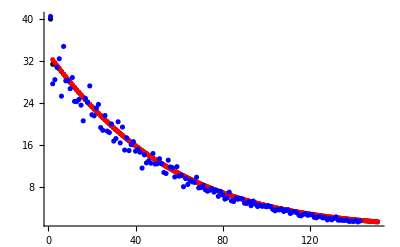

```mathematica
snrnumppl=ListPlot[Table[800*Sqrt[zpnum]*snrnump,{t,0,150}],PlotStyle->Black]; (*Check if plateau only theory matches simulations*)
snrnumpapproxpl=ListPlot[Table[800*Sqrt[zpnum]*snrnumpapprox,{t,0,150}],PlotStyle->Red];
snrpdatapl=ListPlot[snrpdata,PlotStyle->Blue];
Show[snrnumppl,snrnumpapproxpl,snrpdatapl,PlotRange->All,Background->White]
```

```mathematica
wnum
```

0.287666

```mathematica
evr1num
```

{0.680598,0.0317357,0.232451,0.0193195,0.0192004,0.00683798,0.00643126,0.000627063,0.00256414,0.000235139}

```mathematica
evlnum[[1]]
```

{-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228,-0.316228}

General::munfl: -3.11224×10^-31 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.79157×10^-32 2.43346×10^-285 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.9227×10^-33 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -8.68852×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

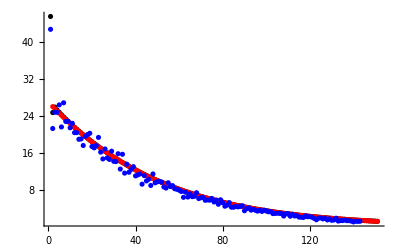

General::munfl: -3.11224×10^-31 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.79157×10^-32 2.43346×10^-285 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.9227×10^-33 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -8.68852×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
snrnumbpl=ListPlot[Table[800*Sqrt[zbnum]*snrnumb,{t,0,150}],PlotStyle->Black] ;(*Check that activity or plateau theory matches simulations*)
snrnumbapproxpl=ListPlot[Table[800*Sqrt[zbnum]*snrnumbapprox,{t,0,150}],PlotStyle->Red];
snrbdatapl=ListPlot[snrbdata,PlotStyle->Blue];
Show[snrnumbpl,snrnumbapproxpl,snrbdatapl,PlotRange->All,Background->White]
snrnumbexp=Table[800*Sqrt[zbnum]*snrnumb,{t,0,150}];
snrnumbapproxexp=Table[800*Sqrt[zbnum]*snrnumbapprox,{t,0,150}];
```

```mathematica
datasig=Import["BTSPCA3_uncorr_N800_10logN_5logN_c8_30r_sig.mat"];
```

```mathematica
sigbdata=datasig[[1]][[1]]; (*Checking signal only*)

sigpdata=datasig[[3]][[1]];
```

General::munfl: -3.11224×10^-31 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.79157×10^-32 2.43346×10^-285 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.9227×10^-33 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -8.68852×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.13958×10^-21)^16 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

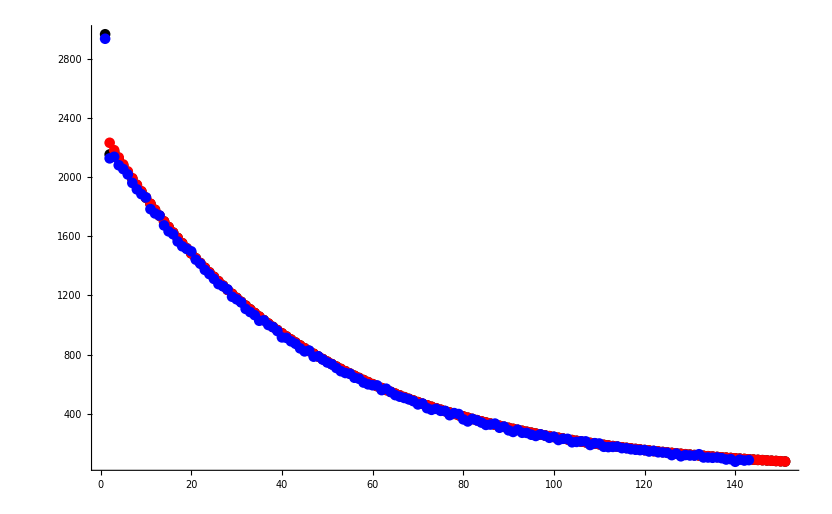

```mathematica
signumppl=ListPlot[Table[800^2*zpnum*signump,{t,0,150}],PlotStyle->Black];
signumpapproxpl=ListPlot[Table[800^2*zpnum*signumpapprox,{t,0,150}],PlotStyle->Red];
sigpdatapl=ListPlot[sigpdata,PlotStyle->Blue];
Show[signumppl,signumpapproxpl,sigpdatapl,PlotRange->All,Background->White]
```

General::munfl: -3.11224×10^-31 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.79157×10^-32 2.43346×10^-285 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.9227×10^-33 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -8.68852×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.13958×10^-21)^16 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

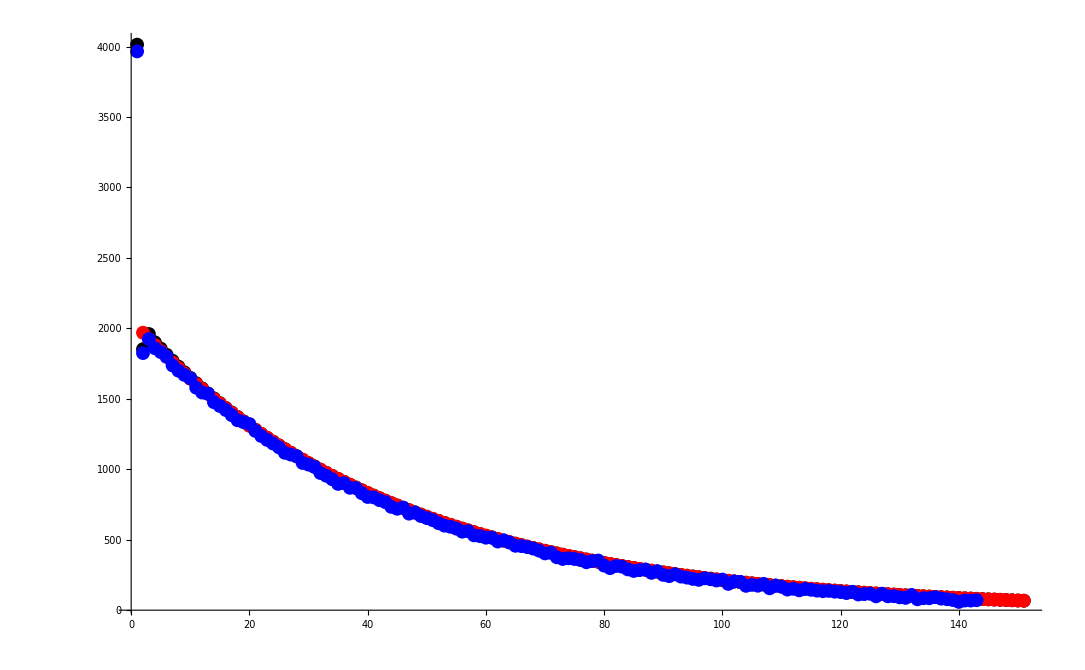

```mathematica
signumbpl=ListPlot[Table[800^2*zbnum*signumb,{t,0,150}],PlotStyle->Black];
signumbapproxpl=ListPlot[Table[800^2*zbnum*signumbapprox,{t,0,150}],PlotStyle->Red];
sigbdatapl=ListPlot[sigbdata,PlotStyle->Blue];
Show[signumbpl,signumbapproxpl,sigbdatapl,PlotRange->All,Background->White]
```

```mathematica
datavar=Import["BTSPCA3_uncorr_N800_10logN_5logN_c8_30r_var.mat"];
```

```mathematica
varbdata=datavar[[1]][[1]];

varpdata=datavar[[3]][[1]];
```

General::munfl: -3.11224×10^-31 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.79157×10^-32 2.43346×10^-285 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.9227×10^-33 (-7.16844×10^-283) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -8.68852×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.23684×10^-15 (-6.3839×10^-303) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

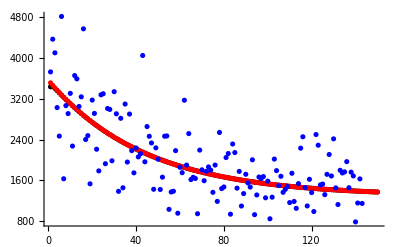

```mathematica
varnumppl=ListPlot[Table[800^2*zpnum*pwnump(1-fp^2*pwnump) /. fp->.084,{t,1,150}],PlotStyle->Black];
varnumpapproxpl=ListPlot[Table[800^2*zpnum*pwnumpapprox(1-fp^2*pwnumpapprox)/.fp->.084,{t,1,150}],PlotStyle->Red];
varpdatapl=ListPlot[varpdata,PlotStyle->Blue];
Show[varnumppl,varnumpapproxpl,varpdatapl,PlotRange->All]
```

```mathematica
snrnumbapproxexp[[1]]=snrnumbapprox0*800*Sqrt[zbnum]
Export["snr_btsp_uncorr_N800_10logN_5logN_c8.csv",snrnumbexp];
Export["snrapprox_btsp_uncorr_N800_10logN_5logN_c8.csv",snrnumbapproxexp];
Export["snrdata_btsp_uncorr_N800_10logN_5logN_c8.csv",snrbdata];
```

45.6158

```mathematica
m=M/.fu->(1-c)fa/.fd->(1-c)(1-fa);
MatrixForm[m]
```

((1-(1-c) fa) (1-fp^2) | (1-c) (1-fa) (1-fp^2) | 0 | (1-(1-c) fa) fp | (1-(1-c) fa) fp | (1-c) (1-fa) fp | (1-(1-c) fa) (2 fp-fp^2) | (1-c) (1-fa) fp | (1-c) (1-fa) (2 fp-fp^2) | (1-c) (1-fa) (2 fp-fp^2)
(1-c) fa (1-fp) | (1-(1-c) (1-fa)) (1-fp) | 0 | (1-c) fa fp | (1-c) fa | (1-(1-c) (1-fa)) fp | (1-c) fa | (1-(1-c) (1-fa)) fp | 1-(1-c) (1-fa) | 1-(1-c) (1-fa)
0 | 0 | (1-(1-c) fa) (1-fp)^2 | (1-(1-c) fa) (1-fp)^2 | (1-(1-c) fa) (1-fp)^2 | (1-c) (1-fa) (1-fp)^2 | (1-(1-c) fa) (1-fp)^2 | (1-c) (1-fa) (1-fp)^2 | (1-c) (1-fa) (1-fp)^2 | (1-c) (1-fa) (1-fp)^2
0 | 0 | (1-(1-c) fa) (1-fp) fp | (1-(1-c) fa) (1-fp) fp | 0 | (1-c) (1-fa) (1-fp) fp | 0 | (1-c) (1-fa) (1-fp) fp | 0 | 0
0 | 0 | (1-(1-c) fa) (1-fp) fp | 0 | (1-(1-c) fa) (1-fp) fp | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-c) fa (1-fp)^2 | (1-c) fa (1-fp)^2 | 0 | (1-(1-c) (1-fa)) (1-fp)^2 | 0 | (1-(1-c) (1-fa)) (1-fp)^2 | 0 | 0
(1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-c) fa (1-fp) fp | (1-c) fa (1-fp) fp | 0 | (1-(1-c) (1-fa)) (1-fp) fp | 0 | (1-(1-c) (1-fa)) (1-fp) fp | 0 | 0
(1-c) fa (1-fp) fp | (1-(1-c) (1-fa)) (1-fp) fp | (1-c) fa (1-fp) fp | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-c) fa fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ppost= (* Projection operator for postsynaptic plateau exposure*)Transpose[{{fp(1-fp)(1-fu),0,0,0,0,0,fp^2(1-fu),0,fp(1-fp)fu,fu*fp^2},{fp(1-fp)fd,0,0,0,0,0,fp^2*fd,0,fp(1-fp)(1-fd),fp^2(1-fd)},{0,0,0,0,fp(1-fp)(1-fu),0,fp^2(1-fu),0,fp(1-fp)fu,fp^2*fu},{fp(1-fu),fp*fu,0,0,0,0,0,0,0,0},{fp^2(1-fu),fp*fu,0,0,fp(1-fp)(1-fu),0,0,0,0,0},{fp*fd,fp(1-fd),0,0,0,0,0,0,0,0},{fp(1-fu),fp*fu,0,0,0,0,0,0,0,0},{fp*fd,fp(1-fd),0,0,0,0,0,0,0,0},{fp*fd,fp*(1-fd),0,0,0,0,0,0,0,0},{fp*fd,fp(1-fd),0,0,0,0,0,0,0,0}}]/.fu->(1-c)fa /.fd->(1-c)(1-fa);
```

```mathematica
MatrixForm[ppost]
```

((1-(1-c) fa) (1-fp) fp | (1-c) (1-fa) (1-fp) fp | 0 | (1-(1-c) fa) fp | (1-(1-c) fa) fp^2 | (1-c) (1-fa) fp | (1-(1-c) fa) fp | (1-c) (1-fa) fp | (1-c) (1-fa) fp | (1-c) (1-fa) fp
0 | 0 | 0 | (1-c) fa fp | (1-c) fa fp | (1-(1-c) (1-fa)) fp | (1-c) fa fp | (1-(1-c) (1-fa)) fp | (1-(1-c) (1-fa)) fp | (1-(1-c) (1-fa)) fp
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-(1-c) fa) (1-fp) fp | 0 | (1-(1-c) fa) (1-fp) fp | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa (1-fp) fp | (1-(1-c) (1-fa)) (1-fp) fp | (1-c) fa (1-fp) fp | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-c) fa fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ppreb= (* Projection operator for presynaptic activity or plateau exposure *)Transpose[{{fp(1-fp)(1-fu),(1-fp)fu,0,0,0,0,fp^2(1-fu),0,fp(1-fp)fu,fp^2*fu},{fd*fp(1-fp),(1-fp)(1-fd),0,0,0,0,fp^2*fd,0,(1-fd)fp(1-fp),fp^2(1-fd)},{0,0,0,fp(1-fp)(1-fu),0,fu(1-fp)^2,fp^2(1-fu),fp*fu(1-fp),fp(1-fp)fu,fp^2*fu},{fp^2(1-fu),fp*fu,0,fp(1-fp)(1-fu),0,fu(1-fp)^2,0,fp(1-fp)fu,0,0},{fp(1-fu),fu,0,0,0,0,0,0,0,0},{fp^2*fd,fp(1-fd),0,fp(1-fp)fd,0,(1-fp)^2(1-fd),0,fp(1-fp)(1-fd),0,0},{fp(1-fu),fu,0,0,0,0,0,0,0,0},{fp^2*fd,fp(1-fd),0,fp(1-fp)fd,0,(1-fp)^2(1-fd),0,fp(1-fp)(1-fd),0,0},{fp*fd,(1-fd),0,0,0,0,0,0,0,0},{fp*fd,1-fd,0,0,0,0,0,0,0,0}}] /.fu->(1-c)fa/.fd->(1-c)(1-fa);
```

```mathematica
MatrixForm[ppreb]
```

((1-(1-c) fa) (1-fp) fp | (1-c) (1-fa) (1-fp) fp | 0 | (1-(1-c) fa) fp^2 | (1-(1-c) fa) fp | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp | (1-c) (1-fa) fp^2 | (1-c) (1-fa) fp | (1-c) (1-fa) fp
(1-c) fa (1-fp) | (1-(1-c) (1-fa)) (1-fp) | 0 | (1-c) fa fp | (1-c) fa | (1-(1-c) (1-fa)) fp | (1-c) fa | (1-(1-c) (1-fa)) fp | 1-(1-c) (1-fa) | 1-(1-c) (1-fa)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-(1-c) fa) (1-fp) fp | (1-(1-c) fa) (1-fp) fp | 0 | (1-c) (1-fa) (1-fp) fp | 0 | (1-c) (1-fa) (1-fp) fp | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-c) fa (1-fp)^2 | (1-c) fa (1-fp)^2 | 0 | (1-(1-c) (1-fa)) (1-fp)^2 | 0 | (1-(1-c) (1-fa)) (1-fp)^2 | 0 | 0
(1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-c) fa (1-fp) fp | (1-c) fa (1-fp) fp | 0 | (1-(1-c) (1-fa)) (1-fp) fp | 0 | (1-(1-c) (1-fa)) (1-fp) fp | 0 | 0
(1-c) fa (1-fp) fp | (1-(1-c) (1-fa)) (1-fp) fp | (1-c) fa (1-fp) fp | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-c) fa fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Total[ppreb]//Simplify
```

{(-1+c) fa (-1+fp)+fp,fa+c (-1+fa) (-1+fp)+fp-fa fp,(-1+c) fa (-1+fp)+fp,(-1+c) fa (-1+fp)+fp,(-1+c) fa (-1+fp)+fp,fa+c (-1+fa) (-1+fp)+fp-fa fp,(-1+c) fa (-1+fp)+fp,fa+c (-1+fa) (-1+fp)+fp-fa fp,fa+c (-1+fa) (-1+fp)+fp-fa fp,fa+c (-1+fa) (-1+fp)+fp-fa fp}

```mathematica
pprep=(* Projection operator for presynaptic plateau exposure *)Transpose[{{fp(1-fp)(1-fu),fp(1-fp)fu,0,0,0,0,fp^2(1-fu),0,0,fp^2*fu},{fp(1-fp)fd,fp(1-fp)(1-fd),0,0,0,0,fp^2*fd,0,0,fp^2(1-fd)},{0,0,0,0,0,fp(1-fp)(1-fu),fp^2(1-fu),fp(1-fp)fu,0,fp^2*fu},{fp^2*fd,fp^2(1-fd),0,0,0,fp(1-fp)fd,0,fp(1-fp)(1-fd),0,0},{fp(1-fu),fp*fu,0,0,0,0,0,0,0,0},{fp^2(1-fu),fp^2*fu,0,0,0,fp(1-fp)(1-fu),0,fp(1-fp)fu,0,0},{fp(1-fu),fp*fu,0,0,0,0,0,0,0,0},{fp^2*fd,fp^2(1-fd),0,0,0,fp(1-fp)fd,0,fp(1-fp)(1-fd),0,0},{fp*fd,fp(1-fd),0,0,0,0,0,0,0,0},{fp*fd,fp(1-fd),0,0,0,0,0,0,0,0}}] /.fu->(1-c)fa/.fd->(1-c)(1-fa);
```

```mathematica
MatrixForm[pprep]
```

((1-(1-c) fa) (1-fp) fp | (1-c) (1-fa) (1-fp) fp | 0 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp | (1-(1-c) fa) fp^2 | (1-(1-c) fa) fp | (1-c) (1-fa) fp^2 | (1-c) (1-fa) fp | (1-c) (1-fa) fp
(1-c) fa (1-fp) fp | (1-(1-c) (1-fa)) (1-fp) fp | 0 | (1-(1-c) (1-fa)) fp^2 | (1-c) fa fp | (1-c) fa fp^2 | (1-c) fa fp | (1-(1-c) (1-fa)) fp^2 | (1-(1-c) (1-fa)) fp | (1-(1-c) (1-fa)) fp
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-(1-c) fa) (1-fp) fp | (1-c) (1-fa) (1-fp) fp | 0 | (1-(1-c) fa) (1-fp) fp | 0 | (1-c) (1-fa) (1-fp) fp | 0 | 0
(1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-c) fa (1-fp) fp | (1-(1-c) (1-fa)) (1-fp) fp | 0 | (1-c) fa (1-fp) fp | 0 | (1-(1-c) (1-fa)) (1-fp) fp | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-c) fa fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Total[pprep]//Simplify
```

{fp,fp,fp,fp,fp,fp,fp,fp,fp,fp}

```mathematica
psimp=fp^2*(m/.fp->1); (* Projection operator for simultaneous presynaptic plateau and postsynaptic plateau *)
```

```mathematica
MatrixForm[psimp]
```

(0 | 0 | 0 | (1-(1-c) fa) fp^2 | (1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-c) (1-fa) fp^2 | (1-c) (1-fa) fp^2
0 | 0 | 0 | (1-c) fa fp^2 | (1-c) fa fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-c) fa fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-(1-c) (1-fa)) fp^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-c) fa fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* x0b={fp(fd(evr1[[6]]+evr1[[8]]+evr1[[9]]+evr1[[10]])+(1-fu)(evr1[[4]]+evr1[[5]]+evr1[[7]])),
(1-fd)(evr1[[6]]+evr1[[8]]+evr1[[9]]+evr1[[10]])+fu(evr1[[4]]+evr1[[5]]+evr1[[7]]),
0,
0,
0,
0,
(fp)((1-fu)(evr1[[1]]+evr1[[3]])+fd(evr1[[2]])),
0,
(1-fp)(fu(evr1[[1]]+evr1[[3]])+(1-fd)evr1[[2]]),
fp(fu(evr1[[1]]+evr1[[3]])+(1-fd)evr1[[2]])}  /. fd->(1-c)(1-fa) /.fu->(1-c)fa; *)
```

```mathematica
psimb=  (* Projection operator for simultaneous presynaptic activity or plateau and postsynaptic plateau *){{0,0,0,fp^2(1-fu),fp^2(1-fu),fp^2*fd,fp^2(1-fu),fp^2*fd,fp^2*fd,fp^2*fd},{0,0,0,fp*fu,fp*fu,fp(1-fd),fp*fu,fp(1-fd),fp(1-fd),fp(1-fd)},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{fp^2(1-fu),fp^2*fd,fp^2(1-fu),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{fp(1-fp)fu,fp(1-fp)(1-fd),fp(1-fp)fu,0,0,0,0,0,0,0},{fp^2*fu,fp^2(1-fd),fp^2*fu,0,0,0,0,0,0,0}}/.fu->(1-c)fa/.fd->(1-c)(1-fa);
```

```mathematica
MatrixForm[psimb]
```

(0 | 0 | 0 | (1-(1-c) fa) fp^2 | (1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-c) (1-fa) fp^2 | (1-c) (1-fa) fp^2
0 | 0 | 0 | (1-c) fa fp | (1-c) fa fp | (1-(1-c) (1-fa)) fp | (1-c) fa fp | (1-(1-c) (1-fa)) fp | (1-(1-c) (1-fa)) fp | (1-(1-c) (1-fa)) fp
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-(1-c) fa) fp^2 | (1-c) (1-fa) fp^2 | (1-(1-c) fa) fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa (1-fp) fp | (1-(1-c) (1-fa)) (1-fp) fp | (1-c) fa (1-fp) fp | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa fp^2 | (1-(1-c) (1-fa)) fp^2 | (1-c) fa fp^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Total[psimb]//Simplify
```

{fp ((-1+c) fa (-1+fp)+fp),fp (fa+c (-1+fa) (-1+fp)+fp-fa fp),fp ((-1+c) fa (-1+fp)+fp),fp ((-1+c) fa (-1+fp)+fp),fp ((-1+c) fa (-1+fp)+fp),fp (fa+c (-1+fa) (-1+fp)+fp-fa fp),fp ((-1+c) fa (-1+fp)+fp),fp (fa+c (-1+fa) (-1+fp)+fp-fa fp),fp (fa+c (-1+fa) (-1+fp)+fp-fa fp),fp (fa+c (-1+fa) (-1+fp)+fp-fa fp)}

```mathematica
mnumc0=m/.fp->.084/.c->0/.fa->.042 ;
ppostnumc0=ppost /.fp->.084/.c->0/.fa->.042 ;
pprebnumc0=ppreb /.fp->.084/.c->0/.fa->.042 ;
evr1numc0=evr1/.fp->.084/.c->0/.fa->.042 ;
psimbnumc0=psimb/.fp->.084/.c->0/.fa->.042 ;
mtnumc0=Table[Which[t==0,IdentityMatrix[10],t≠0,MatrixPower[mnumc0,t]],{t,0,150}];
```

```mathematica
compbnumc0=Indexed[mtnumc0,tpost+1].ppostnumc0.Indexed[mtnumc0,tpre-tpost ].pprebnumc0.evr1numc0;
```

```mathematica
copmbnumc0=Indexed[mtnumc0,tpre+1].pprebnumc0.Indexed[mtnumc0,tpost-tpre].ppostnumc0.evr1numc0;
```

```mathematica
cosbnumc0=Indexed[mtnumc0,tpost+1].psimbnumc0.evr1numc0;
```

```mathematica
xdnumbc0[t1_,t2_]=Which[t1==t2,cosbnumc0/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2 ,t1<t2,copmbnumc0/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2,t1>t2,(compbnumc0/(.084(.084+.042-.084*.042))) /.tpre->t1/.tpost->t2];
```

```mathematica
pwbc0=Table[1-(xdnumbc0[t1,t2])[[1]]-(xdnumbc0[t1,t2])[[2]],{t1,0,100},{t2,0,100}];
```

```mathematica
Export["pwdtb_btsptcorr_fp084_fa042_c0.csv",pwbc0];
```

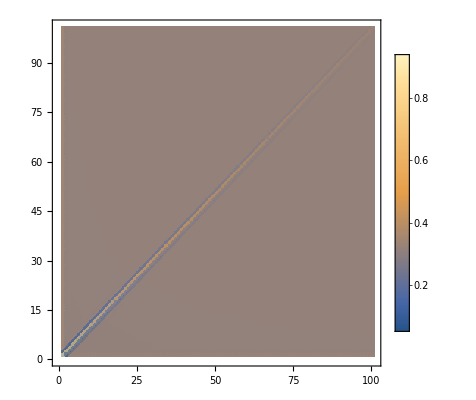

```mathematica
ListDensityPlot[pwbc0,PlotLegends->Automatic,PlotRange->{0,1}]
```

```mathematica
mnumc8=m/.fp->.084/.c->0.8/.fa->.042 ;
ppostnumc8=ppost /.fp->.084/.c->0.8/.fa->.042 ;
pprebnumc8=ppreb /.fp->.084/.c->0.8/.fa->.042 ;
evr1numc8=evr1/.fp->.084/.c->0.8/.fa->.042 ;
psimbnumc8=psimb/.fp->.084/.c->0.8/.fa->.042 ;
mtnumc8=Table[Which[t==0,IdentityMatrix[10],t≠0,MatrixPower[mnumc8,t]],{t,0,150}];
```

```mathematica
compbnumc8=Indexed[mtnumc8,tpost+1].ppostnumc8.Indexed[mtnumc8,tpre-tpost ].pprebnumc8.evr1numc8;
```

```mathematica
copmbnumc8=Indexed[mtnumc8,tpre+1].pprebnumc8.Indexed[mtnumc8,tpost-tpre].ppostnumc8.evr1numc8;
```

```mathematica
cosbnumc8=Indexed[mtnumc8,tpost+1].psimbnumc8.evr1numc8;
```

```mathematica
xdnumbc8[t1_,t2_]=Which[t1==t2,cosbnumc8/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2 ,t1<t2,copmbnumc8/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2,t1>t2,(compbnumc8/(.084(.084+.042-.084*.042))) /.tpre->t1/.tpost->t2];
```

```mathematica
pwbc8=Table[1-(xdnumbc8[t1,t2])[[1]]-(xdnumbc8[t1,t2])[[2]],{t1,0,100},{t2,0,100}];
Export["pwdtb_btsptcorr_fp084_fa042_c8.csv",pwbc8];
```

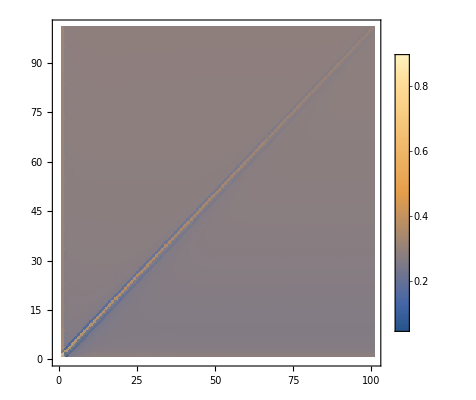

```mathematica
ListDensityPlot[pwbc8,PlotLegends->Automatic,PlotRange->{0,1}]
```

```mathematica
(* This section makes the theoretical calculation for the data plotted in Fig 7A *)
fpnum=.0836;
fanum=.0836;
btsp23=Range[91];
btsp24=Range[91];
btsp23minusw=Range[91];
btsp24minusw=Range[91];
For[i=1,i<92,i++,
cnum=.01*(i-1);
mnumcx=m/.fp->fpnum/.c->cnum/.fa->fanum;
evalsnumcx=Eigenvalues[mnumcx];
evlnumcx=Eigenvectors[Transpose[mnumcx]];
evrnumcx=Eigenvectors[mnumcx];
evrnum1cx=evrnumcx[[1]]/Total[evrnumcx[[1]]];
ppostnumcx=ppost /.fp->fpnum/.c->cnum/.fa->fanum ;
pprebnumcx=ppreb /.fp->fpnum/.c->cnum/.fa->fanum;
psimbnumcx=psimb/.fp->fpnum/.c->cnum/.fa->fanum ;
mtnumcx=Table[Which[t==0,IdentityMatrix[10],t≠0,MatrixPower[mnumcx,t]],{t,0,150}];
copmbnumcx=Indexed[mtnumcx,tpre+1].pprebnumcx.Indexed[mtnumcx,tpost-tpre].ppostnumcx.evrnum1cx;
compbnumcx=Indexed[mtnumcx,tpost+1].ppostnumcx.Indexed[mtnumcx,tpre-tpost ].pprebnumcx.evrnum1cx;
cosbnumcx=Indexed[mtnumcx,tpost+1].psimbnumcx.evrnum1cx;
xdnumbcx[t1_,t2_]=Which[t1==t2,cosbnumcx/(fp(fp+fa-fp*fa))/.tpre->t1 /.tpost->t2 /. fp->fpnum /.fa-> fanum ,t1<t2,copmbnumcx/(fp(fp+fa-fp*fa))/.tpre->t1 /.tpost->t2/. fp->fpnum /.fa-> fanum ,t1>t2,(compbnumcx/(fp(fp+fa-fp*fa))) /.tpre->t1/.tpost->t2 /. fp->fpnum /.fa-> fanum ];
(*pwbcx=Table[1-(xdnumbcx[t1,t2])[[1]]-(xdnumbcx[t1,t2])[[2]],{t1,0,100},{t2,0,100}];*)
btsp23[[i]]=1-(xdnumbcx[5,6])[[1]]-(xdnumbcx[5,6])[[2]];
btsp24[[i]]=1-(xdnumbcx[5,7])[[1]]-(xdnumbcx[5,7])[[2]];
meanw=1-evrnum1cx[[1]]-evrnum1cx[[2]];
btsp23minusw[[i]]=btsp23[[i]]-meanw;
btsp24minusw[[i]]=btsp24[[i]]-meanw;
]
```

```mathematica
Export["btsp23_fp0836_fa0836.csv",btsp23];
Export["btsp24_fp0836_fa0836.csv",btsp24];
Export["btsp23minusw_fp0836_fa0836.csv",btsp23minusw];
Export["btsp24minusw_fp0836_fa0836.csv",btsp24minusw];
```